# Linear operators

## Linear operators

#### Reflection against the x axis:

```mathematica
Op1=({{1, 0}, {0, -1}});
```

#### Reflection against the y axis:

```mathematica
Op2=({{-1, 0}, {0, 1}});
```

#### Reflection against the origin axis:

```mathematica
Op3=({{-1, 0}, {0, -1}});
```

#### Projection onto the x axis:

```mathematica
Op4=({{1, 0}, {0, 0}});
```

#### Projection onto the y axis:

```mathematica
Op5=({{0, 0}, {0, 1}});
```

#### Scaling by 2 in all directions:

```mathematica
Op6=({{2, 0}, {0, 2}});
```

#### Horizontal shear mapping:

```mathematica
Op7=({{1, 2}, {0, 1}});
```

#### Vertical shear mapping:

```mathematica
Op8=({{1, 0}, {2, 1}});
```

#### Squeeze mapping:

```mathematica
Op9=({{2, 0}, {0, 1/2}});
```

#### Rotation by θ degrees counterclockwise:

```mathematica
θ=45 Degree;
```

```mathematica
Op10=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
```

## Graph

```mathematica
Op=Op2;
```

```mathematica
g1={Sin[t]+2,Cos[t]+2};
```

```mathematica
g2=Op.g1
```

{-2-Sin[t],2+Cos[t]}

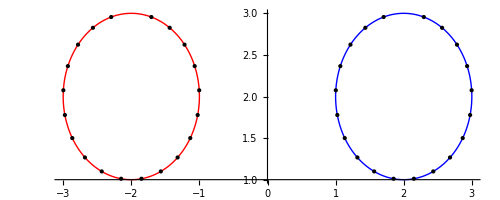

```mathematica
ParametricPlot[{g1,g2},{t,0,2π},
PlotRange->All,
Mesh->20,
MeshStyle->PointSize[Medium],
PlotStyle->{{Blue,Thick},{Red,Thick}}]
```